```mathematica
s=NDSolve[{0.01*y''[x]+y'[x]+y[x]^2==0,{y[0]==0,y'[0]==1/0.01}},y,{x,0,3}]
```

{{y→InterpolatingFunction[{{0., 3.}}, <>]}}

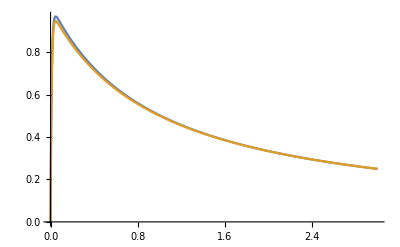

```mathematica
Plot[{Evaluate[y[x]/.s],1/(x+1)-(Exp[-x/0.01])},{x,0,3},PlotRange->All]
```

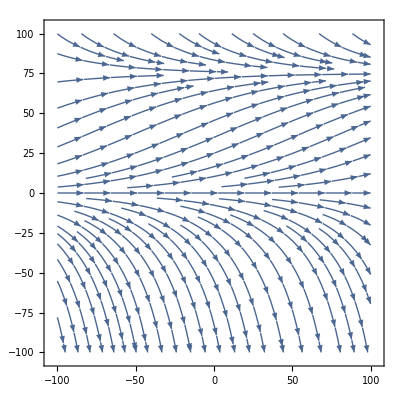

```mathematica
StreamPlot[{1,0.0225*y-0.0003*y^2},{x,-100,100},{y,-100,100}]
```

```mathematica
Series[1/(1+(1/x-a)^4),{x,0,5}]
```

x^4+4 a x^5+O[x]^6